## B

```mathematica
SetDirectory[NotebookDirectory[]];
gini[x_]:=N[Sum[Sum[Abs[x[[i]]-x[[j]]],{i,1,Length[x]}],{j,1,Length[x]}]/(2*Length[x]*Sum[x[[i]],{i,1,Length[x]}])]
max[x_]:=N[Max[x]/Total[x]]
```

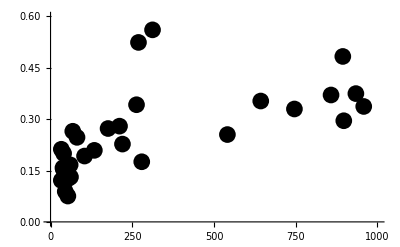

```mathematica
giniList={};
c2=RGBColor[85/255,85/255,85/255];
Do[
c=Import["chambers//c"<>ToString[ii]<>".dat","List"];
AppendTo[giniList,{Total[c],Max[c]/Total[c]}];
,{ii,1,21}];
Do[
s=Import["chambers//s"<>ToString[ii]<>".dat","List"];
AppendTo[giniList,{Total[s],Max[s]/Total[s]}];
,{ii,1,11}]
figB=ListPlot[giniList,PlotStyle->{Black,PointSize->0.03},PlotRange->{{0,1000},{0,0.6}}]
```

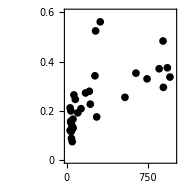

```mathematica
FigB=plot[
{figB},
xTicks->{0,250,500,750,1000},
yTicks->{0,0.2,0.4,0.6},
tickLength->0.12,
plotRange->{{0,1000},{0,0.6}},
plotDimensions->{5,5},
plotMargins->{0.9,0.2,1.1,0.4},
plotLabels->{
Row[{Style["Cell number"]}],
Row[{Style["Largest cluster fractional size"]}]},
labelsDistance->{0.55,0.75},
plotTitle->True,
titleText->"",
titleDistance->0.3,
fontMain->7,
fontName->"Helvetica"
]
```

```mathematica
Export["figs//SYS_Fig2B.pdf",FigB]
```

figs//SYS_Fig2B.pdf

## C

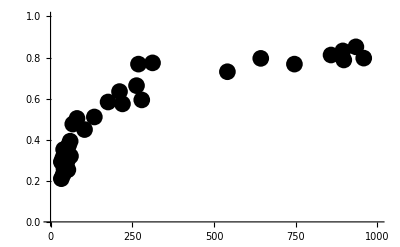

```mathematica
giniList={};
Do[
c=Import["chambers//c"<>ToString[ii]<>".dat","List"];
AppendTo[giniList,{Total[c],gini[c]}];
,{ii,1,21}];
Do[
s=Import["chambers//s"<>ToString[ii]<>".dat","List"];
AppendTo[giniList,{Total[s],gini[s]}];
,{ii,1,11}];
figC=ListPlot[giniList,PlotStyle->{Black,PointSize->0.03},PlotRange->{{0,1000},{0,1}}]
```

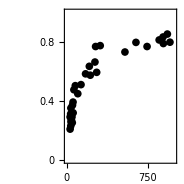

```mathematica
FigC=plot[
{figC},
xTicks->{0,250,500,750,1000},
yTicks->{0,0.2,0.4,0.6,0.8,1},
tickLength->0.12,
plotRange->{{0,1000},{0,1}},
plotDimensions->{5,5},
plotMargins->{0.9,0.2,1.1,0.4},
plotLabels->{
Row[{Style["Cell number"]}],
Row[{Style["Gini coefficient "],Style["G",Italic]}]},
labelsDistance->{0.55,0.75},
plotTitle->True,
titleText->"",
titleDistance->0.3,
fontMain->7,
fontName->"Helvetica"
]
```

```mathematica
Export["figs//SYS_Fig2C.pdf",FigC]
```

figs//SYS_Fig2C.pdf